## Lesson

Specify a circle and display it:



```mathematica
Graphics[Circle[]]
```

A disk is a filled circle:



```mathematica
Graphics[Disk[]]
```

Regular polygon with n sides:

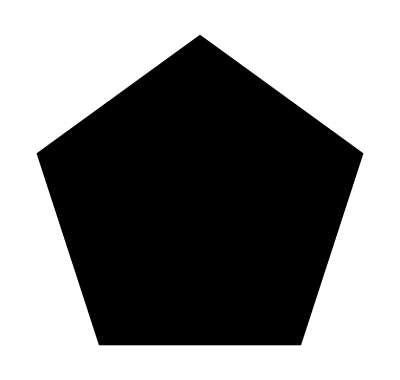

```mathematica
Graphics[RegularPolygon[5]]
```

Display 3D objects:

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

## Questions

Q1. Use RegularPolygon to draw a triangle.



```mathematica
Graphics[RegularPolygon[3]]
```

Q2. Make graphics of a red circle.

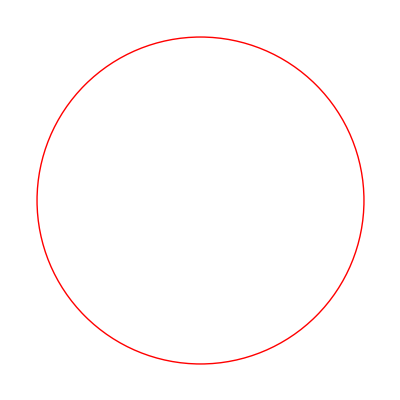

```mathematica
Graphics[Style[Circle[],Red]]
```

Q3. Make a red octagon.

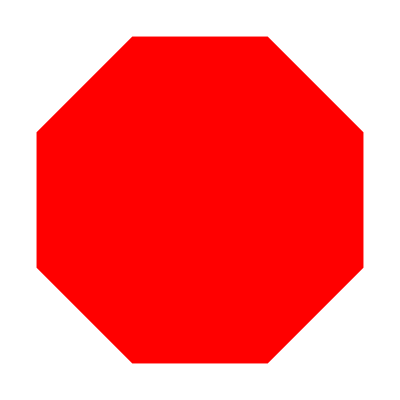

```mathematica
Graphics[Style[RegularPolygon[8],Red]]
```

Q4. Make a list whose elements are disks with hues varying from 0 to 1 in steps of 0.1


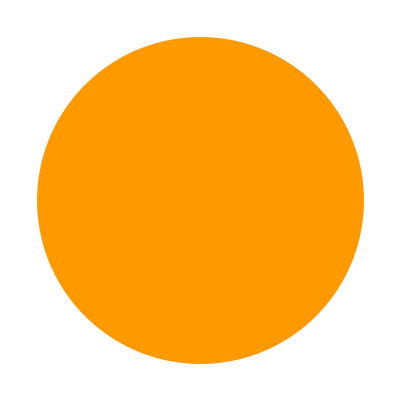
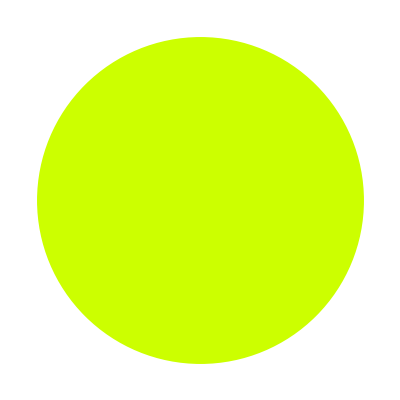
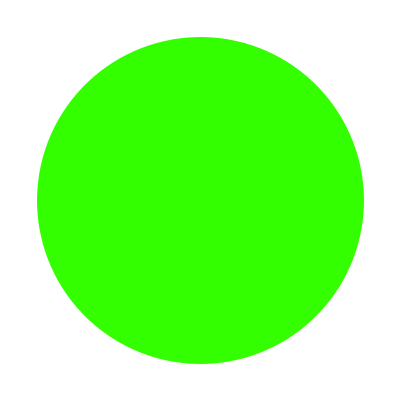
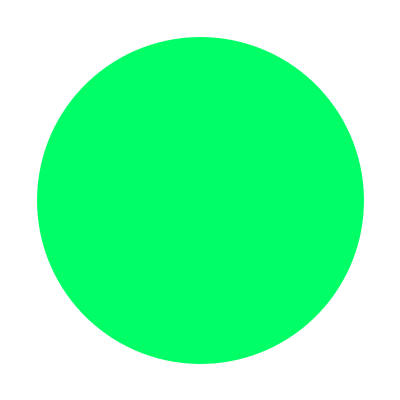
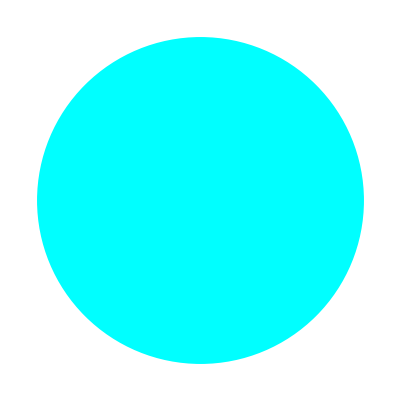
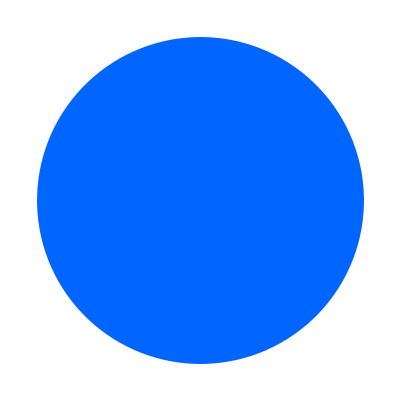
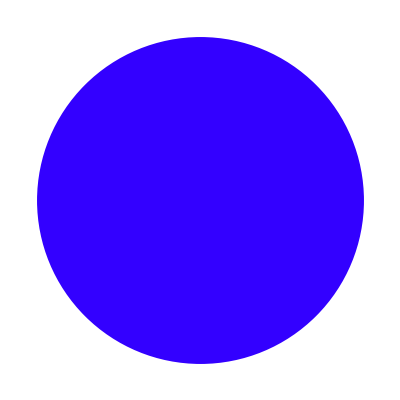
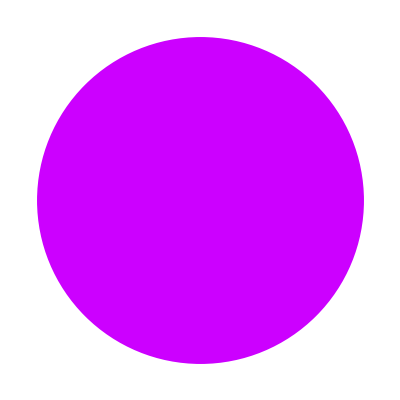
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[Disk[],Hue[i]]],{i,0,1,0.1}]
```

Q5. Make a column of a red and a green triangle.

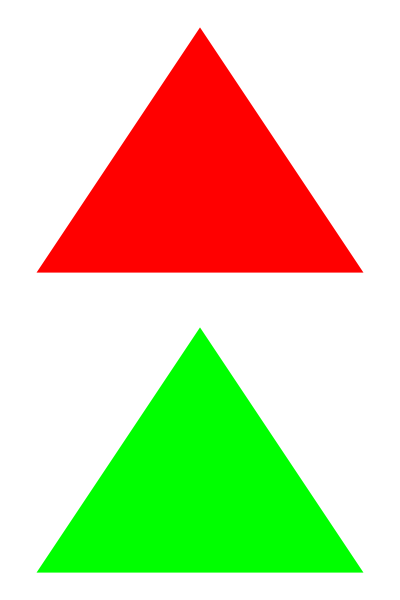

```mathematica
Column[{Graphics[Style[RegularPolygon[3],Red]],Graphics[Style[RegularPolygon[3],Green]]}]
```

Q6. Make a list giving the regular polygons with 5 through 10 sides, with each polygon being colored pink.

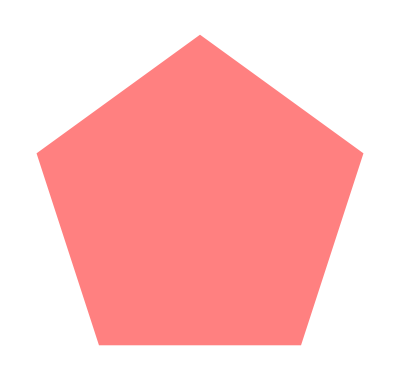
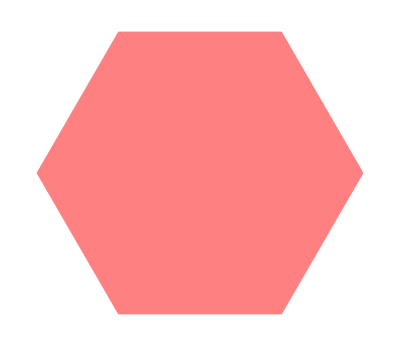
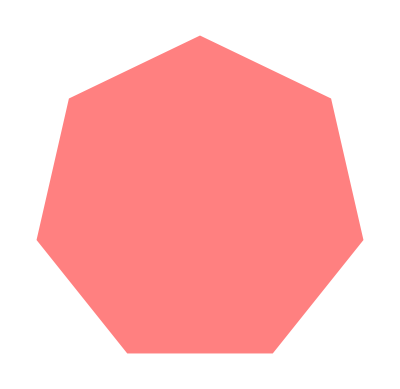
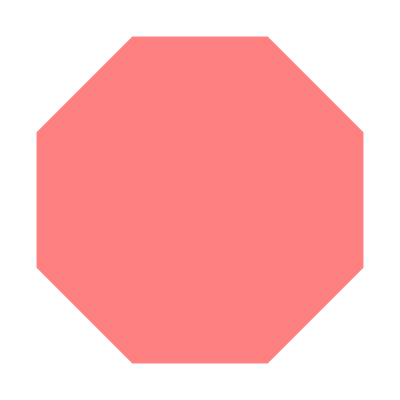
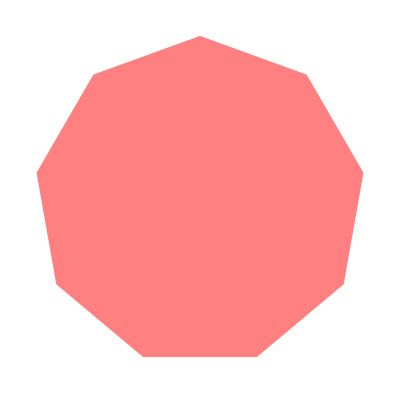
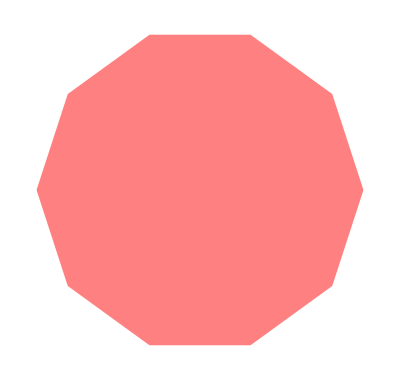

```mathematica
Graphics[Style[RegularPolygon[#],Pink]]&/@Range[5,10]
```

Q7. Make a graphic of a purple cylinder.

```mathematica
Graphics3D[Style[Cylinder[],Purple]]
```

-Graphics3D-

Q8. Make a list of polygons with 8, 7, 6, ... , 3 sides, and colored with RandomColor, then show them all overlaid with the triangle on top (hint: apply Graphics to the list).

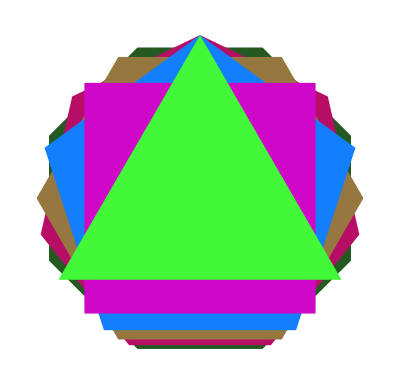

```mathematica
Graphics[Table[Style[RegularPolygon[i],RandomColor[]],{i,8,3,-1}]]
```

## Extended Questions

+Q1. Make a list of 10 regular pentagons with random colors.

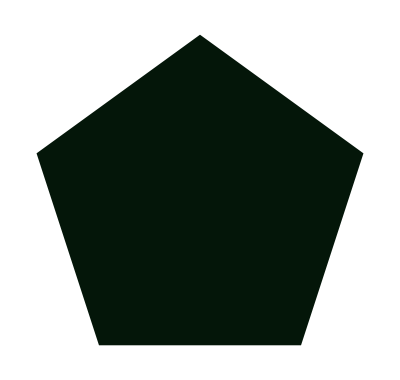
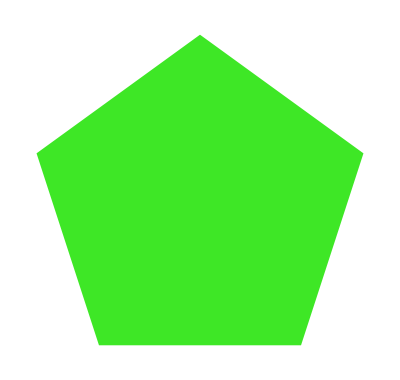
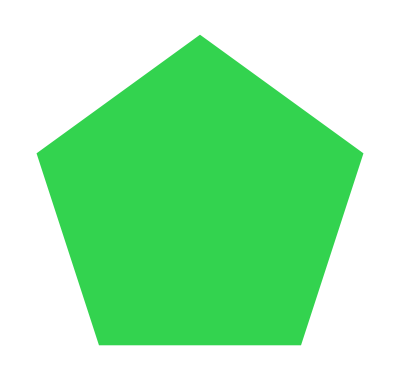
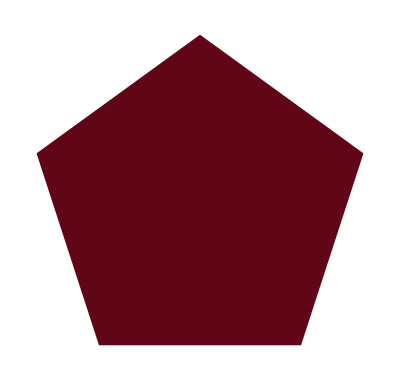
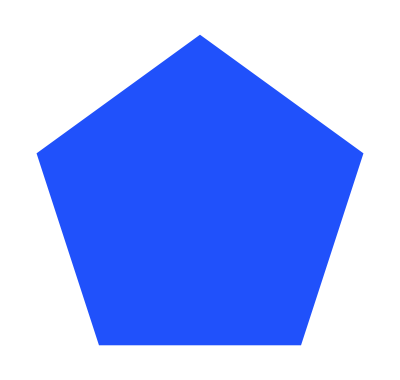
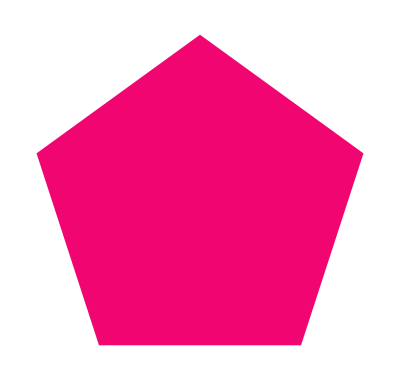
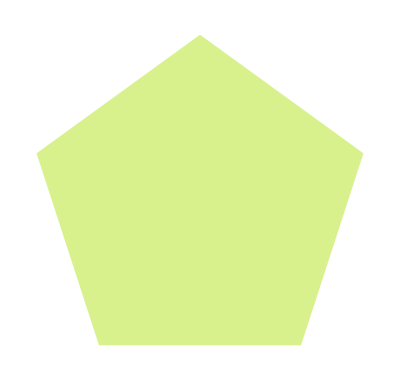
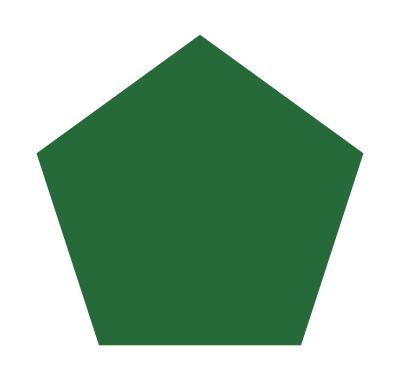

```mathematica
Table[Graphics[Style[RegularPolygon[5],RandomColor[]]],10]
```

+Q2. Make a list of a 20-sided regular polygon and a disk.

```mathematica
{Graphics[RegularPolygon[20]],Graphics[Disk[]]}
```

{-Graphics-,-Graphics-}

+Q3. Make a list of polygons with 10, 9, ... , 3 sides.

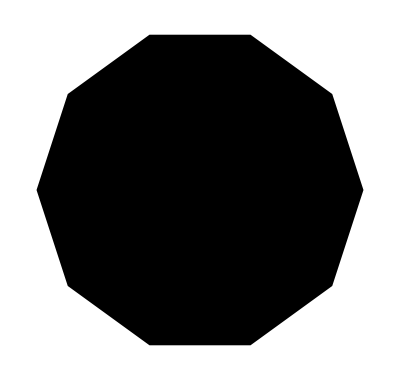
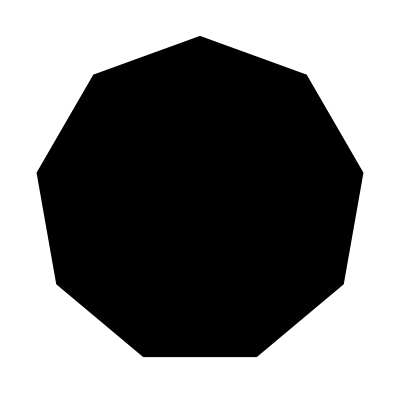
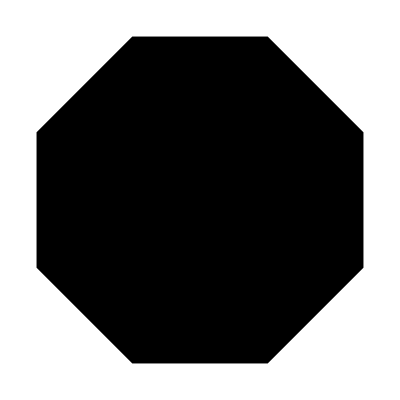
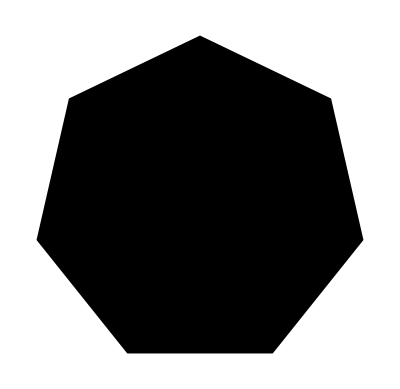
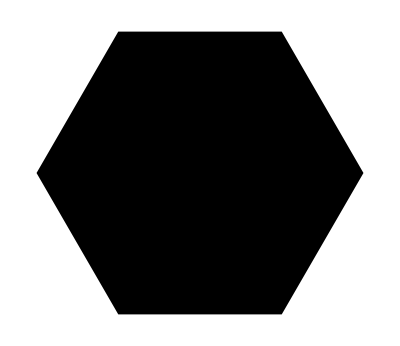

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[RegularPolygon[#]]&/@Range[10,3,-1]
```